```mathematica
1q
```

I need a better summary notebook laying out the models for acute/chronic bistability as I start wanting to actually write a paper on all of this!

The NIH grant included these two models. The first is a model with immune-mediated feedbacks causing bistability. This model is a simplification of the model in Yates et al. 2000. Andy’s model was looking at Th1-Th2 feedbacks, specifically, but also included activation-induced cell death. The version I have included here is a much-simplified version of that model that basically only includes two key processes necessary to produce bistability: auto-stimulation (which would come about through cytokine-T cell positive feedback) and activation-induced cell death.

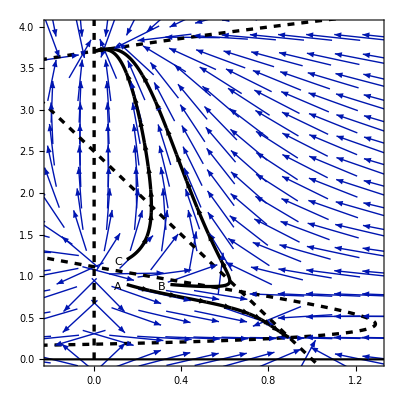

```mathematica
(* The model *)
dp2=(1-p) p α-p t μ;
dt2=(γ+t (t-δ+p σ-t^2 χ))/δ;
(* Isoclines *)
pisocline=Solve[dp2==0,p][[2,1,2]];
tisocline=Solve[dt2==0,p][[1,1,2]];
(* Parameters that produce bistability *)
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.15};
(* Individual simulations showing alternative outcomes from different initial conditions of parasite and immunity *)
sol1=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.35,t[0]==0.9},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.15,t[0]==0.9},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.15,t[0]==1.2},{p,t},{T,0,50}];
(* Plot *)
Show[VectorPlot[{dp2/.params,dt2/.params},{p,-2,2},{t,0,8},VectorScale->{0.028,0.6,None},VectorStyle->{Gray},VectorPoints->32],
ListLinePlot[Table[{tisocline/.params,t},{t,0.01,20,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black},PlotRange->All],
ListLinePlot[Table[{pisocline/.params,t},{t,-2,15,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{p,0},{p,-2,8,0.01}],PlotStyle->{Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[Text[Style[A,Large],{0.11,0.87}]],
Graphics[Text[Style[B,Large],{0.31,0.87}]],
Graphics[Text[Style[C,Large],{0.11,1.17}]],
PlotRange->{{-0.2,1.3},{0,4}}]
```

The second model is focused on parasite-mediated feedbacks. This is a model that I developed that includes a very simple immune-parasite model with an additionally function that allows for the parasite to suppress the immune response.

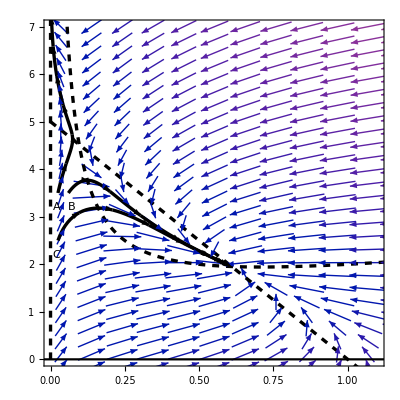

```mathematica
(* The model *)
dt=γ+β p-ν t-α p/(1+p) t;
dp=λ p (1-p)-κ p t;
(* The isoclines *)
tisocline=Solve[dt==0,t][[1,1,2]]//Simplify;
pisocline=Solve[dp==0,t][[1,1,2]];
(* Parameters that produce bistability *)
params={β->2,γ->1,κ->0.8,λ->4,α->3,ν->0.0001};
(* Individual simulations showing alternative outcomes from different initial conditions of parasite and immunity *)sol1=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==3.5},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.06,t[0]==3.5},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==2.5},{p,t},{T,0,50}];
(* Plotting *)
Show[VectorPlot[{dp/.params,dt/.params},{p,-1,2},{t,-1,7},VectorScale->{0.015,0.5,None},VectorStyle->{GrayLevel[0.8]},VectorPoints->30],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.001}],PlotStyle->{Thickness[0.006],Dashed,Black},PlotRange->All],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{p,0},{p,-1,8,0.01}],PlotStyle->{Medium,Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,10,0.1}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#3&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,8,0.1}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#3&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[Text[Style[A,Large],{0.02,3.2}]],
Graphics[Text[Style[B,Large],{0.07,3.2}]],
Graphics[Text[Style[C,Large],{0.02,2.2}]],
PlotRange->{{0,1.1},{0,7}}]
```

One possibility would be to use these two models separately. 

An additional possibility that would be easier, in some sense, would be to build on some existing models. In particular, a type III functional response can generate bistability under a particularly fluky situation - if the immune response can be treated as a constant, then a type III functional response on the parasite would generate bistability between a low parasite biomass and a high parasite biomass.

```mathematica
dp=λ p (1-p/K)-(a p^2 t)/(1+a Th p^2);
```

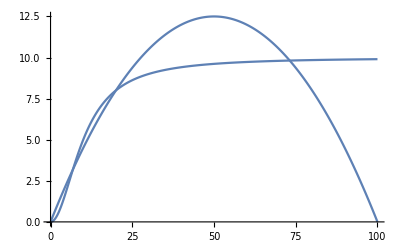

```mathematica
Show[ListLinePlot[Table[{p,(λ p (1-p/K)/.{λ->0.5,K->100})},{p,0,100,0.1}]],
ListLinePlot[Table[{p,((a p^2 t)/(1+a Th p^2)/.{a->0.005,Th->2,t->20})},{p,0,100,0.1}]]]
```

```mathematica
(* Here are the equilibria *)
equil=Solve[dp==0,p]/.{λ->0.5,K->100,a->0.005,Th->2,t->20}
(* The middle two are stable *)
D[dp,p]/.{λ->0.5,K->100,a->0.005,Th->2,t->20}/.equil
```

{{p→0},{p→6.83375-3.55271×10^-15 ⅈ},{p→73.1662+0. ⅈ},{p→20.+0. ⅈ}}

{0.5,-0.203417-5.47231×10^-17 ⅈ,-0.236583+0. ⅈ,0.14+0. ⅈ}

Actually, I don’t even think you need a Type III response for this. You could get it with a Type II response as well.

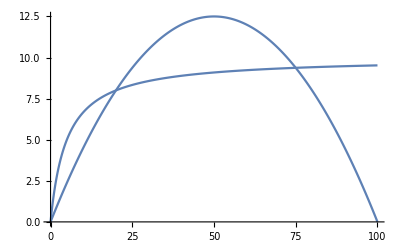

```mathematica
Show[ListLinePlot[Table[{p,(λ p (1-p/K)/.{λ->0.5,K->100})},{p,0,100,0.1}]],
ListLinePlot[Table[{p,((a p t)/(1+a Th p)/.{a->0.1,Th->2,t->20})},{p,0,100,0.1}]]]
```

```mathematica
(* Here are the equilibria *)
equil=Solve[dp==0,p]/.{λ->0.5,K->100,a->0.1,Th->2,t->20}
(* The middle two are stable *)
D[dp,p]/.{λ->0.5,K->100,a->0.1,Th->2,t->20}/.equil
```

{{p→0},{p→0.25255+0. ⅈ},{p→72.4033-3.55271×10^-15 ⅈ},{p→27.3442+3.55271×10^-15 ⅈ}}

{0.5,-0.487436+0. ⅈ,-0.224295+3.54885×10^-17 ⅈ,0.221732-3.36626×10^-17 ⅈ}

But if you add in a dynamic immune response, I’m pretty sure this will go away, as I know that it will for the case with a Type II functional response. 

I can do a little digging to ensure this. To stay more consistent with the parasite-mediated feedback model, I will continue to assume logistic growth of the parasite and see if a Type III functional response is sufficient.

```mathematica
dt=γ+ϵ κ[p] t-ν t;
dp=λ p (1-p)-κ[p] t;
```

What is required for there to be bistability between a disease-free equilibrium and a disease present equilibrium?

Stability of the acute infection equilibrium requires that λ-(γ κ'[0])/ν<0. Note that this somewhat restricts the possible functional forms for the immune system’s functional response for bistability to be possible. In particular, any function that has a slope of 0 at p = 0 (which includes a Type III functional response) can never be bistable between an acute and chronic infection. A Type II functional response, however, would work.

```mathematica
acuteEquil=Append[Solve[(dt/.{κ[p]->0})==0,t]⟦1⟧,p->0]
MatrixForm[J=D[{dt,dp},{{t,p}}]]
Simplify[Eigenvalues[J/.acuteEquil/.κ[0]->0]]
```

{t→γ/ν,p→0}

(-ν+ϵ κ[p] | t ϵ κ'[p]
-κ[p] | (1-p) λ-p λ-t κ'[p])

{-ν,λ-(γ κ'[0])/ν}

```mathematica
chronicEquil=Solve[dt==0,t]⟦1⟧
Tr[J/.chronicEquil] (* needs to be negative *)
Det[J/.chronicEquil]
```

{t→γ/(ν-ϵ κ[p])}

(1-p) λ-p λ-ν+ϵ κ[p]-(γ κ'[p])/(ν-ϵ κ[p])

-λ ν+2 p λ ν+ϵ λ κ[p]-2 p ϵ λ κ[p]+(γ ν κ'[p])/(ν-ϵ κ[p])

```mathematica
(* Assume that the trace is negative, as needed *)
(* What is necessary for the determinant to be positive *)
```

```mathematica
Expand[-ν Tr[J/.chronicEquil]] (* this must all be positive, since the trace is negative *)
(* Can I show this inequality to hold? If so, then the chronic equilibrium will be stable *)
Simplify[Expand[-ν Tr[J/.chronicEquil]] <Det[J/.chronicEquil] ]
```

-λ ν+2 p λ ν+ν^2-ϵ ν κ[p]+(γ ν κ'[p])/(ν-ϵ κ[p])

ν^2+ϵ ((-1+2 p) λ-ν) κ[p]<0

#### What makes the most sense?

I think what makes the most sense is to approach this with an eye on Th1-Th2 interaction. I think that anything is just going to be unrealistic. You can still get bistability with a more complex immune response. Basically, if the system has an inherent bias towards a Th1 response, then a low initial parasite biomass will be insufficient to prevent Th1 polarization, whereas a higher parasite biomass will allow it.

Ed Schrom’s model does not include a parasite in it; instead it models the expression levels of transcription factors T-bet (TF1) and GATA-3 (TF2) and the expression levels of the cytokines IFNg (CY1) and IL4 (CY2). T-cells expressing T-bet are Th1 cells and T-cells expressing GATA-3 are Th2 cells; these cells also express the key cytokines that help to drive the polarization of other T-cells. That is, a naive T-cell will be bound by both IFNg and IL4, which will drive internal expression of T-bet and GATA-3, which will then drive the expression of IFNg and IL4. 

This will have to be integrated into a model that allows for dynamics of the T-cell populations and the parasite. That’s no small task, actually.

```mathematica
dTF1dt=(b+(p1 TF1^hp)/(P1^hp+TF1^hp)) (X2^hx/(X2^hx+TF2^hx))+((s1 CY1^hs)/(S1^hs+CY1^hs))(Z2^hz/(Z2^hz+CY2^hz))-dTF1 TF1
dTF2dt=(b+(p2 TF2^hp)/(P2^hp+TF2^hp)) (X1^hx/(X1^hx+TF1^hx))+((s2 CY2^hs)/(S2^hs+CY2^hs))(Z1^hz/(Z1^hz+CY1^hz))-dTF2 TF2
dCY1dt=((a1 TF1^ha)/(A1^ha+TF1^ha))(R2^hr/(R2^hr+TF2^hr))(U2^hu/(U2^hu+CY2^hu))-dCY1 CY1
dCY2dt=((a2 TF2^ha)/(A2^ha+TF2^ha))(R1^hr/(R1^hr+TF1^hr))(U1^hu/(U1^hu+CY1^hu))-dCY2 CY2
```

-dTF1 TF1+((b+(p1 TF1^hp)/(P1^hp+TF1^hp)) X2^hx)/(TF2^hx+X2^hx)+(CY1^hs s1 Z2^hz)/((CY1^hs+S1^hs) (CY2^hz+Z2^hz))

-dTF2 TF2+((b+(p2 TF2^hp)/(P2^hp+TF2^hp)) X1^hx)/(TF1^hx+X1^hx)+(CY2^hs s2 Z1^hz)/((CY2^hs+S2^hs) (CY1^hz+Z1^hz))

-CY1 dCY1+(a1 R2^hr TF1^ha U2^hu)/((A1^ha+TF1^ha) (R2^hr+TF2^hr) (CY2^hu+U2^hu))

-CY2 dCY2+(a2 R1^hr TF2^ha U1^hu)/((R1^hr+TF1^hr) (A2^ha+TF2^ha) (CY1^hu+U1^hu))

```mathematica
Solve[{dCY1dt==0,dCY2dt==0}/.hu->1,{CY1,CY2}]
```

{{CY1→1/(2 dCY1 dCY2 U2)(-(a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))+(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))-dCY1 dCY2 U1 U2-√((4 a1 dCY1 dCY2^2 R2^hr TF1^ha U1 U2^2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+((a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))-(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+dCY1 dCY2 U1 U2)^2)),CY2→(a2 R1^hr TF2^ha U1)/(dCY2 (R1^hr+TF1^hr) (A2^ha+TF2^ha) (U1+1/(2 dCY1 dCY2 U2)(-(a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))+(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))-dCY1 dCY2 U1 U2-√((4 a1 dCY1 dCY2^2 R2^hr TF1^ha U1 U2^2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+((a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))-(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+dCY1 dCY2 U1 U2)^2))))},{CY1→1/(2 dCY1 dCY2 U2)(-(a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))+(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))-dCY1 dCY2 U1 U2+√((4 a1 dCY1 dCY2^2 R2^hr TF1^ha U1 U2^2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+((a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))-(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+dCY1 dCY2 U1 U2)^2)),CY2→(a2 R1^hr TF2^ha U1)/(dCY2 (R1^hr+TF1^hr) (A2^ha+TF2^ha) (U1+1/(2 dCY1 dCY2 U2)(-(a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))+(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))-dCY1 dCY2 U1 U2+√((4 a1 dCY1 dCY2^2 R2^hr TF1^ha U1 U2^2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+((a2 dCY1 R1^hr TF2^ha U1)/((R1^hr+TF1^hr) (A2^ha+TF2^ha))-(a1 dCY2 R2^hr TF1^ha U2)/((A1^ha+TF1^ha) (R2^hr+TF2^hr))+dCY1 dCY2 U1 U2)^2))))}}

Assumptions underlying these parameter choices can be found in Ed’s paper, but here are the parameters. The key biological points that Ed makes that would be relevant for a simplified model are:
- early TF production is CY-independent and symmetric
- Hill exponents = 2 for processes that are observed to have switch-like behavior, such as TF self-regulation/self-promotion in the absence of CY
- blocking a TF1/2 promoter reduces TF1/2 production more than it enhance TF2/1 production
- Hill exponents = 1 for processes that are observed to change gradually, such as CY promotion/inhibition of TF production and TF promotion/inhibition of CY production
- CY promotion of TF is much stronger than CY inhibition of TF production, CY2 inhibition of TF1 is stronger than CY1 inhibition of TF2
- TF-driven CY expression is invoked long after TF-driven TF expression has reached steady state
- CY1 and CY2 production rates are both more impacted by TF2 than TF1

The other key point is that there are a few quantities that depend on “cell-volume of extracellular space [cvpc]”. This is because TF are measured on a per-cell basis, whereas secreted cytokines are measured on a concentration basis (e.g., ng/mL), so Ed had to figure out a conversion. He defined concentration to be the “number of cytokine molecules per cell-volume of extracellular space.” Given the known molecular weight of a cytokine and the known volume of a Th cell, the number of cytokine molecules per cell-volume of extracellular space is easily converted to ng/mL. The key here is that cell density controls the ratio of the volume occupied by cells to the total volume including extracellular space, which he calls the packing efficiency (packing efficiency = cell density * cellular volume). He then converts packing efficiency into the number of cell-volumes of extracellular space per Th cell (cvpc = (1-packing efficiency)/(packing efficiency). The higher the cvpc, the lower the secretion and removal rate of cytokines.

Thus, one thing that is worth looking at is how cytokine secretion changes with cell density. If cell density is 10^6 Th cells/mL, and cell volume is 180 μm^3 = 180 μm^3/10^12 μm^3/mL = 1.8 x 10^-10 mL, then cpvc = (1-10^6 1.8 10^-10)/(10^6 1.8 10^-10)=5554.56; if cell density is 10^9 cells/mL, then cpvc = (1-10^9 1.8 10^-10)/(10^9 1.8 10^-10)=4.56.

```mathematica
N[(1-10^6 180/10^12)/(10^6 180/10^12)]
N[(1-10^9 180/10^12)/(10^9 180/10^12)]
```

5554.56

4.55556

```mathematica
params=
{b->0.2, (* basal TF production rate, [molecules/hr] *)
p1->10, (* maximal TF1 production rate due to the presence of TF1, [molecules/hr] *)
p2->10, (* maximal TF2 production rate due to the presence of TF2, [molecules/hr] *)
P1->10, (* half-maximal copy number for TF1 self-promotion, [molecules] *)
P2->10, (* half-maximal copy number for TF2 self-promotion, [molecules] *)
hp->2,   (* Hill exponent for TF self-promotion [dim] *)
X1->30, (* Half-maximal copy number for TF1 cross-inhibition of TF2 production, [molecules] *)
X2->30, (* Half-maximal copy number for TF2 cross-inhibition of TF1 production, [molecules] *)
hx->2,   (* Hill exponent for TF cross-inhibition [dim] *)
s1->20, (* maximal TF1 production rate due to the presence of CY1, [molecules/hr] *)
s2->20, (* maximal TF2 production rate due to the presence of CY2, [molecules/hr] *)
S1->200, (* half-maximal concentration of CY1 for promotion of TF1 production, [molecules/cell-volume of extracellular space *)
S2->200, (* half-maximal concentration of CY2 for promotion of TF2 production, [molecules/cell-volume of extracellular space *)
hs->1,   (* Hill exponent for CY promotion of TF production *)
Z1->2400, (* half-maximal concentration of CY1 for inhibition of TF2 expression, [molecules/cell-volume of extracellular space *)
Z2->1600, (* half-maximal concentration of CY2 for inhibition of TF1 expression, [molecules/cell-volume of extracellular space *)
hz->1,  (* Hill exponent for CY inhibition of TF production *)
dTF1->0.15, (* degradation rate of TF1 mRNA, [1/hr] *)
dTF2->0.15, (* degradation rate of TF2 mRNA, [1/hr] *)
a1->20 3600/cvpc, (* maximal production rate of CY1, [molecules/cell-volume of extracellular space]*)
a2->20 3600/cvpc, (* maximal production rate of CY2, [molecules/cell-volume of extracellular space]*)
A1->80, (* Half-maximal copy number of TF1 to promote CY1 production, [molecules] *)
A2->80, (* Half-maximal copy number of TF2 to promote CY2 production, [molecules] *)
ha->1, (* Hill exponent for TF promotion of CY production *)
R1->112, (* half-maximal copy number of TF1 to inhibit CY2 production *)
R2->48, (* half-maximal copy number of TF2 to inhibit CY1 production *)
hr->1, (* Hill exponent for TF inhibition of CY production *)
U1->2000, (* half-maximal concentration of CY1 to inhibit production of CY2 *)
U2->2000, (* half-maximal concentration of CY2 to inhibit production of CY1 *)
hu->1, (* Hill exponent for CY inhibition of CY production *)
dCY1->0.8/cvpc+0.015, (* removal rate of CY1, [1/cell volume/hr] *)
dCY2->0.8/cvpc+0.015 (* removal rate of CY2, [1/cell volume/hr] *)
};
```

We can use simulation of these models to get some sense of how long it takes for cytokine secretion to come to an equilibrium at different cell densities. 

At low cell density, it takes quite a long time - thousands of hours.

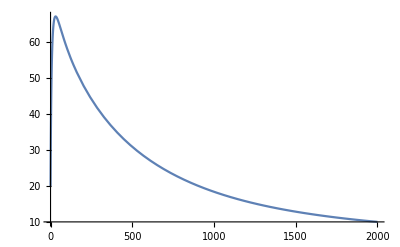

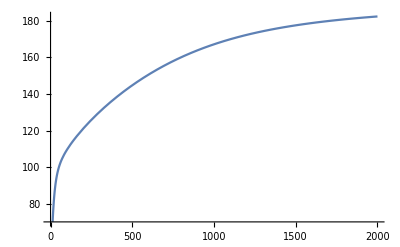

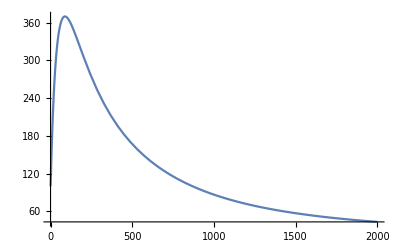

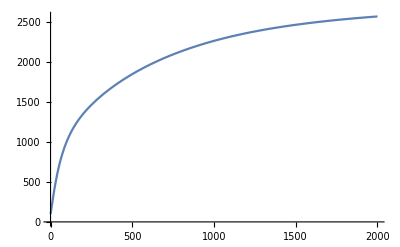

```mathematica
cd=5 10^6;
sol=NDSolve[{TF1'[t]==(dTF1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF2'[t]==(dTF2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY1'[t]==(dCY1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY2'[t]==(dCY2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,2000}];
Plot[TF1[t]/.sol,{t,0,2000}]
Plot[TF2[t]/.sol,{t,0,2000}]
Plot[CY1[t]/.sol,{t,0,2000}]
Plot[CY2[t]/.sol,{t,0,2000}]
```

It’s much faster at higher cell densities. That’s a key thing to note: polarization occurs more quickly as more T cells are recruited. Basically, the immune system makes decisions faster the more T cells there are in an area.  By the time you get to very high T cell populations, polarization can happen within a few days. That makes perfect sense, since the more cells there are, the more they are sending out signals to drive polarization. 

Note, however, that the equilibrium level of cytokine expression is not strongly affected by cell density - it goes up with cell density, but not a lot.

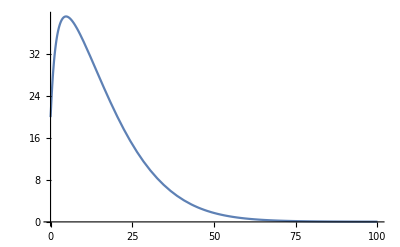

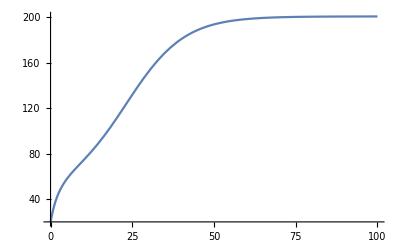

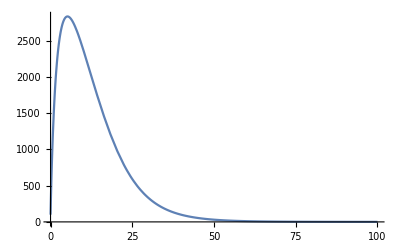

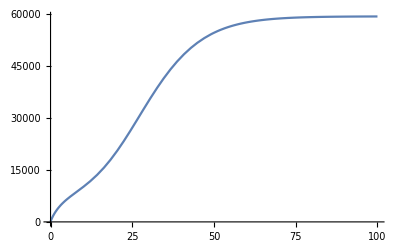

```mathematica
cd=10^9;
sol=NDSolve[{TF1'[t]==(dTF1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF2'[t]==(dTF2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY1'[t]==(dCY1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY2'[t]==(dCY2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}];
Plot[TF1[t]/.sol,{t,0,100}]
Plot[TF2[t]/.sol,{t,0,100}]
Plot[CY1[t]/.sol,{t,0,100}]
Plot[CY2[t]/.sol,{t,0,100}]
```

Here I get the final CY and TF expression across a range of cell densities, from 10^6 to 10^9 cells/mL.

```mathematica
EQbyCD=Table[
{cd,TF1[10000],TF2[10000],CY1[10000],CY2[10000]}/.NDSolve[{TF1'[t]==(dTF1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF2'[t]==(dTF2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY1'[t]==(dCY1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY2'[t]==(dCY2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}],{cd,10^6,10^9,10^6}];
```

You can see that transcription factor expression is, for the most part, insensitive to cell density. Total cytokine is, of course, much more closely related to cell density, and is a saturating function for the cytokine that is being expressed (in this case, CY2).  Thus, if we were going to make a simplified model, you would want cytokine expression to be a saturating function of cell density.

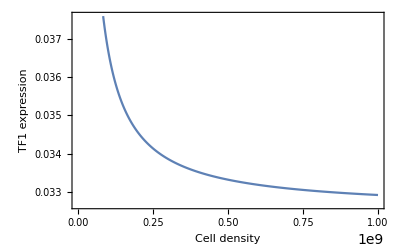

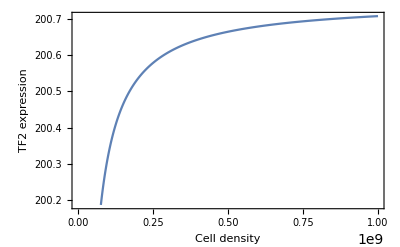

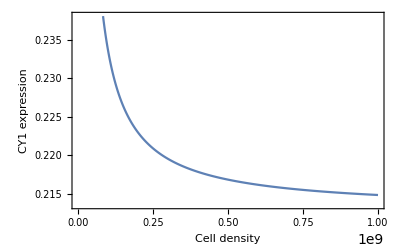

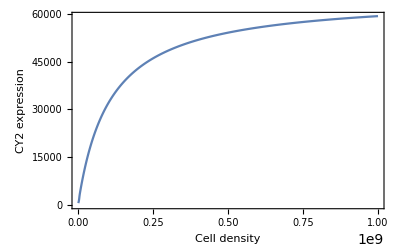

```mathematica
ListLinePlot[EQbyCD[[;;,1,1;;2]],Frame->True,FrameLabel->{"Cell density","TF1 expression"}]
ListLinePlot[EQbyCD[[;;,1,{1,3}]],Frame->True,FrameLabel->{"Cell density","TF2 expression"}]
ListLinePlot[EQbyCD[[;;,1,{1,4}]],Frame->True,FrameLabel->{"Cell density","CY1 expression"}]
ListLinePlot[EQbyCD[[;;,1,{1,5}]],Frame->True,FrameLabel->{"Cell density","CY2 expression"}]
```

But there is something weird going on at low cell densities - not sure if that’s just numerical error or a real signal.

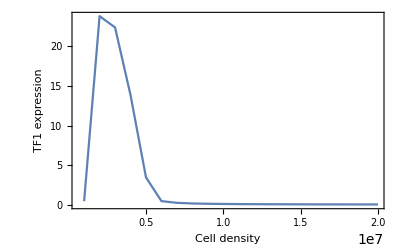

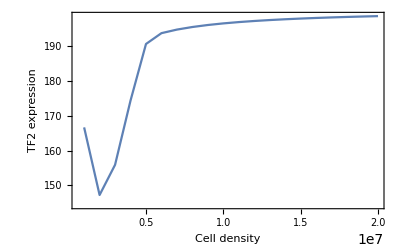

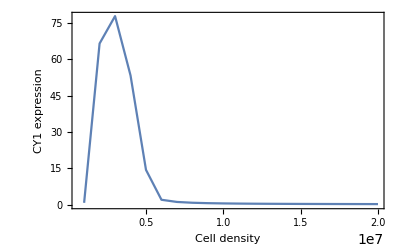

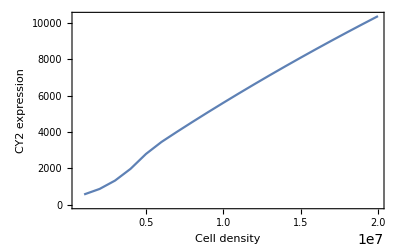

```mathematica
ListLinePlot[EQbyCD[[1;;20,1,1;;2]],PlotRange->All,Frame->True,FrameLabel->{"Cell density","TF1 expression"}]
ListLinePlot[EQbyCD[[1;;20,1,{1,3}]],PlotRange->All,Frame->True,FrameLabel->{"Cell density","TF2 expression"}]
ListLinePlot[EQbyCD[[1;;20,1,{1,4}]],PlotRange->All,Frame->True,FrameLabel->{"Cell density","CY1 expression"}]
ListLinePlot[EQbyCD[[1;;20,1,{1,5}]],PlotRange->All,Frame->True,FrameLabel->{"Cell density","CY2 expression"}]
```

You can also see how long it takes to reach equilibrium as a function of cell density:

```mathematica
timeToEq=Table[0,1000];
For[i=1,i<1001,i++,
cd=Table[c,{c,10^6,10^9,10^6}]⟦i⟧;sol=NDSolve[{TF1'[t]==(dTF1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF2'[t]==(dTF2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY1'[t]==(dCY1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY2'[t]==(dCY2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}];
timeToEq⟦i⟧={cd,First[Position[Table[Abs[1-((CY2[t]/CY2[10000])/.sol)⟦1⟧],{t,10,10000,1}],x_/;x<0.1]][[1]]}
]
```

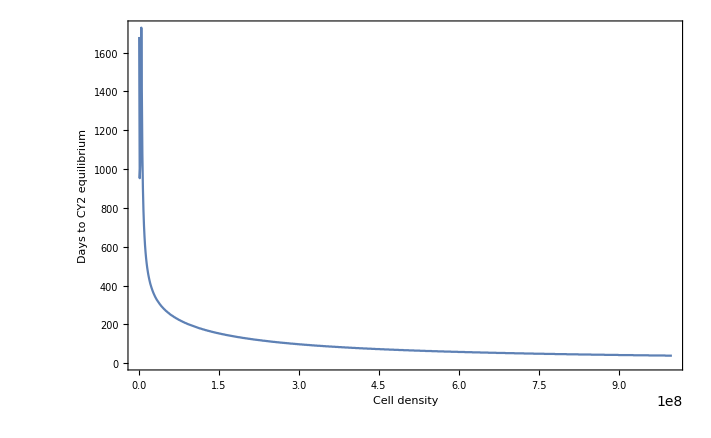

```mathematica
ListLinePlot[timeToEq,Frame->True,FrameLabel->{"Cell density","Days to CY2 equilibrium"},PlotRange->All]
```

One last addition that Ed considers is the effect of instruction by antigen-presenting cells (APCs). “Biologically, APCs provide Th1 or Th2 instructions by secreting Th1- or Th2-driving cytokines directly onto a Th cell surface. Therefore, we included APC instruction by augmenting every appearance of CY1 and CY2 (except decay) in the model equations with constants APC1 and APC2, whose values depend on the frequencies of Type 1 and Type 2 APCs, respectively.”

That leads to the following set of equations:

```mathematica
dTF1dt2=(b+(p1 TF1^hp)/(P1^hp+TF1^hp)) (X2^hx/(X2^hx+TF2^hx))+((s1 (CY1+APC1)^hs)/(S1^hs+(CY1+APC1)^hs))(Z2^hz/(Z2^hz+(CY2+APC2)^hz))-dTF1 TF1;
dTF2dt2=(b+(p2 TF2^hp)/(P2^hp+TF2^hp)) (X1^hx/(X1^hx+TF1^hx))+((s2 (CY2+APC2)^hs)/(S2^hs+(CY2+APC2)^hs))(Z1^hz/(Z1^hz+(CY1+APC1)^hz))-dTF2 TF2;
dCY1dt2=((a1 TF1^ha)/(A1^ha+TF1^ha))(R2^hr/(R2^hr+TF2^hr))(U2^hu/(U2^hu+(CY2+APC2)^hu))-dCY1 CY1;
dCY2dt2=((a2 TF2^ha)/(A2^ha+TF2^ha))(R1^hr/(R1^hr+TF1^hr))(U1^hu/(U1^hu+(CY1+APC1)^hu))-dCY2 CY2;
```

We also have to add terms for APC1 and APC2 to our parameter list. 

However, this is defined in a somewhat obscure way in Ed’s paper: “0.003 or 0.17 * (98% effective concentration of CY): The first term is the per-hour probability of an antigen-specific Th cell encountering a dendritic cell, which ranges from 0.003 to 0.17 at biologically realistic dendritic cell frequencies. The second term assumes the influence of a Type-1 APC is as strong as the concentration of CY1 that would stimulate 98% of Th cells to produce TF1.” The second part of this is ambiguous to me, because it’s unclear if this means: “would stimulate 98% of Th cells to produce TF1 in the absence of any influence from CY2 and TF2” or not. 

Based on an email from Ed, this is how these values were calculated - he did ignore the influence of CY2 and TF1/2:

```mathematica
Solve[((CY1)^hs/(S1^hs+(CY1)^hs)/.params)==0.98,CY1]
Solve[((CY2)^hs/(S2^hs+(CY2)^hs)/.params)==0.98,CY2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{CY1→9800.}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{CY2→9800.}}

```mathematica
params2={b->0.2,p1->10,p2->10,P1->10,P2->10,hp->2,X1->30,X2->30,hx->2,s1->20,s2->20,S1->200,S2->200,hs->1,Z1->2400,Z2->1600,hz->1,dTF1->0.15,dTF2->0.15,a1->72000/cvpc,a2->72000/cvpc,A1->80,A2->80,ha->1,R1->112,R2->48,hr->1,U1->2000,U2->2000,hu->1,dCY1->0.015+0.8/cvpc,dCY2->0.015+0.8/cvpc,APC1->9800,APC2->9800};
```

The first thing to look at is to compare the timecourses of TF and CY expression without and with APCs. Let’s do it for a fairly high cell density (cd = 1e8)

```mathematica
sol1=NDSolve[{TF1'[t]==(dTF1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
TF2'[t]==(dTF2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
CY1'[t]==(dCY1dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
CY2'[t]==(dCY2dt/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}];
sol2=NDSolve[{TF1'[t]==(dTF1dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
TF2'[t]==(dTF2dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
CY1'[t]==(dCY1dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
CY2'[t]==(dCY2dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}/.cd->10^8),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}];
```

You can see that the addition of APCs (both Type 1 and Type 2) makes a co-expression equilibrium much more likely. Without APCs, the equilibrium is Th2 polarized. Now it is much more balanced between the two - the expression of TF2 > TF1, but TF1 >> 0 now.

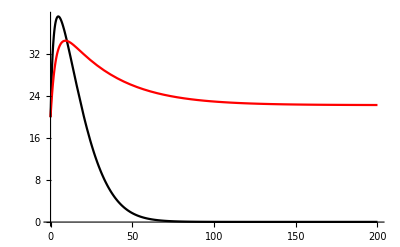

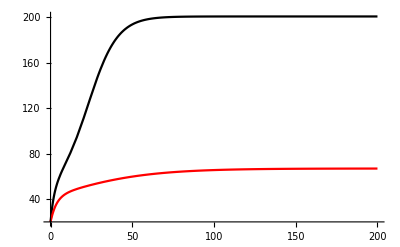

```mathematica
Show[Plot[TF1[t]/.sol1,{t,0,200},PlotRange->All,PlotStyle->Black],
Plot[TF1[t]/.sol2,{t,0,200},PlotRange->All,PlotStyle->{Red}]]
Show[Plot[TF2[t]/.sol1,{t,0,200},PlotRange->All,PlotStyle->Black],
Plot[TF2[t]/.sol2,{t,0,200},PlotRange->All,PlotStyle->{Red}]]
```

A similar pattern holds for the cytokine expression.

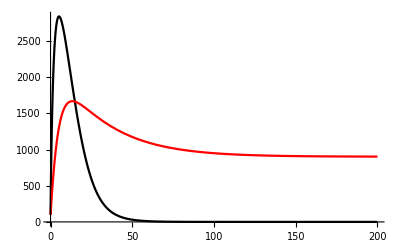

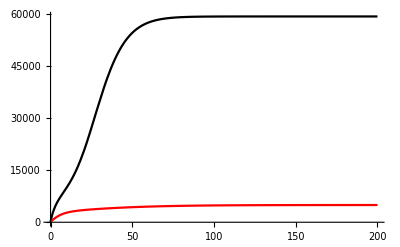

```mathematica
Show[Plot[CY1[t]/.sol1,{t,0,200},PlotRange->All,PlotStyle->Black],
Plot[CY1[t]/.sol2,{t,0,200},PlotRange->All,PlotStyle->{Red}]]
Show[Plot[CY2[t]/.sol1,{t,0,200},PlotRange->All,PlotStyle->Black],
Plot[CY2[t]/.sol2,{t,0,200},PlotRange->All,PlotStyle->{Red}]]
```

```mathematica
EQbyCD2=Table[
{cd,TF1[10000],TF2[10000],CY1[10000],CY2[10000]}/.NDSolve[{TF1'[t]==(dTF1dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF2'[t]==(dTF2dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY1'[t]==(dCY1dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY2'[t]==(dCY2dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}],{cd,10^6,10^9,10^6}];
```

You can see that the addition of antigen presenting cells drastically increases the equilibrium TF1 expression:

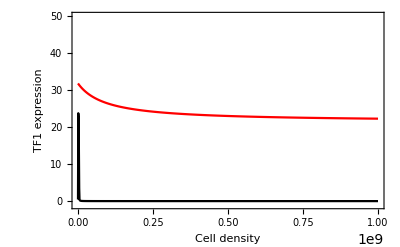

```mathematica
Show[ListLinePlot[EQbyCD[[;;,1,{1,2}]],Frame->True,FrameLabel->{"Cell density","TF1 expression"},PlotStyle->Black,PlotRange->{{10^6,10^9},{-1,50}}],
ListLinePlot[EQbyCD2[[;;,1,{1,2}]],PlotStyle->Red,PlotRange->{{10^6,10^9},{0,50}}]]
```

You can see that the addition of antigen presenting cells drastically decreases the equilibrium TF2 expression:

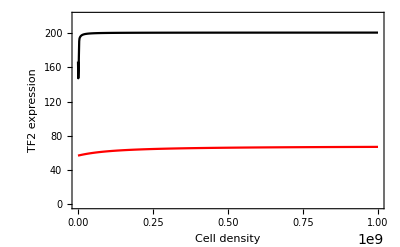

```mathematica
Show[ListLinePlot[EQbyCD[[;;,1,{1,3}]],Frame->True,FrameLabel->{"Cell density","TF2 expression"},PlotStyle->Black,PlotRange->{{10^6,10^9},{-1,220}}],
ListLinePlot[EQbyCD2[[;;,1,{1,3}]],PlotStyle->Red,PlotRange->{{10^6,10^9},{-1,220}}]]
```

This change in TF expression has massive affects on the equilibrium cytokine expression.

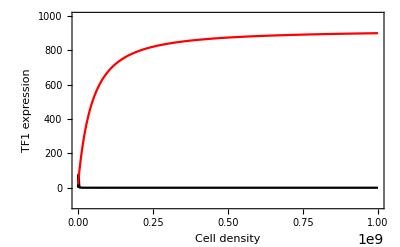

```mathematica
Show[ListLinePlot[EQbyCD[[;;,1,{1,4}]],Frame->True,FrameLabel->{"Cell density","TF1 expression"},PlotStyle->Black,PlotRange->{{10^6,10^9},{-100,1000}}],
ListLinePlot[EQbyCD2[[;;,1,{1,4}]],PlotStyle->Red]]
```

However, the system is still massively dominated by CY2.

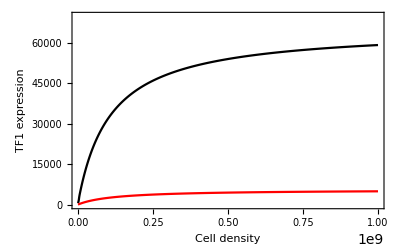

```mathematica
Show[ListLinePlot[EQbyCD[[;;,1,{1,5}]],Frame->True,FrameLabel->{"Cell density","TF1 expression"},PlotStyle->Black,PlotRange->{{10^6,10^9},{-100,70000}}],
ListLinePlot[EQbyCD2[[;;,1,{1,5}]],PlotStyle->Red]]
```

Addition of APCs also has no effect on the timecourse of cytokine.

```mathematica
timeToEq2=Table[0,1000];
For[i=1,i<1001,i++,
cd=Table[c,{c,10^6,10^9,10^6}]⟦i⟧;sol=NDSolve[{TF1'[t]==(dTF1dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF2'[t]==(dTF2dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY1'[t]==(dCY1dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
CY2'[t]==(dCY2dt2/.{TF1->TF1[t],TF2->TF2[t],CY1->CY1[t],CY2->CY2[t]}/.params2/.{cvpc->(1-cd 180/10^12)/(cd 180/10^12)}),
TF1[0]==20,
TF2[0]==20,
CY1[0]==100,
CY2[0]==100
},{TF1,TF2,CY1,CY2},{t,0,10000}];
timeToEq2⟦i⟧={cd,First[Position[Table[Abs[1-((CY2[t]/CY2[10000])/.sol)⟦1⟧],{t,10,10000,1}],x_/;x<0.1]][[1]]}
]
```

In general, and especially at low cell densities, addition of APCs speeds up the approach to equilibrium. At higher cell densities, it has less of an effect, likely because the increase in the abundance of TF1 and CY1 is antagonistic with TF2 and CY2, and that mutual antagonism slows down the approach to equilibrium of the system.

```mathematica
timeToEq2⟦;;,2⟧-timeToEq⟦;;,2⟧
```

{-1536,-952,-937,-1225,-1613,-1270,-953,-775,-662,-582,-523,-477,-441,-411,-386,-365,-347,-330,-317,-304,-293,-282,-274,-265,-258,-250,-244,-237,-232,-226,-220,-216,-211,-207,-203,-200,-196,-193,-189,-186,-183,-180,-177,-175,-172,-170,-167,-164,-163,-160,-158,-156,-155,-152,-150,-149,-147,-145,-143,-141,-140,-138,-137,-136,-134,-133,-131,-130,-129,-127,-126,-125,-124,-122,-121,-120,-119,-118,-117,-115,-114,-114,-112,-111,-111,-109,-108,-108,-107,-106,-104,-104,-103,-102,-102,-101,-100,-99,-99,-98,-97,-96,-96,-95,-94,-93,-93,-92,-91,-90,-90,-89,-88,-87,-86,-87,-86,-85,-84,-84,-83,-83,-82,-81,-81,-80,-80,-79,-78,-78,-78,-77,-76,-76,-76,-75,-74,-74,-73,-73,-73,-72,-71,-71,-71,-70,-70,-69,-69,-68,-68,-68,-67,-67,-66,-65,-66,-65,-65,-64,-64,-63,-63,-63,-62,-62,-61,-61,-60,-61,-60,-60,-59,-59,-58,-59,-58,-58,-57,-57,-56,-56,-56,-56,-55,-55,-54,-54,-54,-53,-54,-53,-53,-52,-52,-51,-51,-51,-51,-51,-50,-50,-50,-49,-49,-48,-49,-49,-48,-48,-47,-47,-47,-46,-47,-46,-46,-46,-45,-45,-45,-44,-44,-45,-44,-44,-44,-43,-43,-43,-42,-42,-41,-42,-42,-42,-41,-41,-41,-40,-40,-40,-39,-40,-40,-39,-39,-39,-38,-38,-38,-37,-37,-38,-38,-37,-37,-37,-36,-36,-36,-36,-35,-35,-35,-35,-35,-35,-35,-34,-34,-34,-34,-33,-33,-33,-34,-33,-33,-33,-33,-32,-32,-32,-31,-31,-31,-31,-31,-31,-31,-31,-31,-30,-30,-30,-30,-29,-29,-29,-29,-28,-29,-29,-29,-29,-28,-28,-28,-28,-27,-27,-27,-27,-27,-26,-26,-27,-27,-27,-26,-26,-26,-26,-25,-25,-25,-25,-25,-24,-24,-24,-25,-25,-24,-24,-24,-24,-24,-24,-23,-23,-23,-23,-23,-22,-22,-22,-23,-23,-22,-22,-22,-22,-22,-22,-21,-21,-21,-21,-21,-21,-20,-20,-20,-20,-21,-21,-20,-20,-20,-20,-20,-20,-19,-19,-19,-19,-19,-19,-18,-18,-18,-18,-18,-19,-18,-18,-18,-18,-18,-18,-18,-17,-17,-17,-17,-17,-17,-16,-16,-16,-16,-16,-16,-17,-16,-16,-16,-16,-16,-16,-16,-15,-15,-15,-15,-15,-15,-15,-14,-14,-14,-14,-14,-14,-14,-15,-14,-14,-14,-14,-14,-14,-14,-14,-13,-13,-13,-13,-13,-13,-13,-12,-12,-12,-12,-12,-12,-12,-12,-13,-12,-12,-12,-12,-12,-12,-12,-12,-11,-11,-11,-11,-11,-11,-11,-11,-11,-10,-10,-10,-10,-10,-10,-10,-10,-11,-10,-10,-10,-10,-10,-10,-10,-10,-10,-9,-9,-9,-9,-9,-9,-9,-9,-9,-8,-8,-8,-8,-8,-8,-8,-8,-8,-9,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-7,-7,-7,-7,-7,-7,-7,-7,-7,-7,-7,-6,-6,-6,-6,-6,-6,-6,-6,-6,-7,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-5,-5,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-2,-2,-2,-2,-2,-2,-2,-2,-2,-3,-3,-3,-3,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10}

From Ed’s model, I have a really good idea about how to extend to a fully dynamic model that considers the dynamics of T cells and parasites. In particular, 
* the dynamics of T cells affect cell density so simply make cell density a dynamic variable;
* the dynamics of the parasite affect APC density so simply make APC density depend on parasite biomass - nix: Andrea says that it is better to think of APC density as fixed - what changes is instead the fraction of those cells that are expressing a particular antigen. In other words, make Th1/Th2 antigen-presenting cells something like  APC2 P/(h+P), where P is the abundance of parasites; 
* the mortality of the parasite should depend on both T cell density and TF expression: T cells expressing the wrong TF (Th1 polarized) will have little to no effect on biomass growth, whereas T cells expressing the right TF (Th2 polarized) will kill the parasite

The questions are the following: 
* How does parasite killing depend on T cell density? 

Thoughts for how to structure our paper:
- Simple model showing that parasite manipulation can lead to bistability between acute and chronic;
- Simple model showing that Th1-Th2 cross-inhibition and self-stimulation can lead to bistability between Th1-biased and Th2-biased.
- Combine simple models to show how parasite manipulation can lead to acute vs chronic via Th1 vs Th2 bias
- Complex model based on Ed’s model showing how that relies on the internal 

Question for Andrea:
- Are you happy with the simple model that we have for immune-mediated feedback (which currently only includes self-stimulation and self-inhibition)? Can I justify the form for self-inhibition, which comes from Andy’s paper that is focused primarily on activation-induced cell death?

#### Th1/Th2 interference

What I want here is the simplest possible model of Th1/Th2 interference that will produce Allee effects. Note that one such model would be based on L-V competition models, but those models don’t always produce bistability. I suppose that’s the point, though, isn’t it?

The Lotka-Volterra competition model is the following

```mathematica
dTh1=r1 Th1 (1-(Th1+a12 Th2)/K1);
dTh2=r2 Th2(1-(Th2+a21 Th1)/K2);
```

Here are the equilibria of that model:

```mathematica
Solve[{dTh1==0,dTh2==0},{Th1,Th2}]
```

{{Th1→0,Th2→K2},{Th1→-(K1-a12 K2)/(-1+a12 a21),Th2→-(-a21 K1+K2)/(-1+a12 a21)},{Th1→0,Th2→0},{Th1→K1,Th2→0}}

The Th1-biased response equilibrium is stable if a21 K1-K2 > 0; the Th2-biased response is stable if K1-a12 K2 < 0. Expressing those in terms of the antagonistic interaction parameters, bistability is possible if a21 K1 > K2 and a12 K2 > K1. To put those conditions biologically: the Th1 has to have a larger negative effect on Th2 than it has on itself, and Th2 has to have a larger negative effect on Th1 than it has on itself.

```mathematica
Eigenvalues[D[{dTh1,dTh2},{{Th1,Th2}}]/.{Th1->K1,Th2->0}]
Eigenvalues[D[{dTh1,dTh2},{{Th1,Th2}}]/.{Th1->0,Th2->K2}]
```

{-r1,-((a21 K1-K2) r2)/K2}

{((K1-a12 K2) r1)/K1,-r2}

This makes it clear why this isn’t a good model for Th1/Th2 responses: Th1 responses don’t have a strong negative impact on themselves, they have a strong negative impact on Th2 and vice versa. Thus we need a different set of equations.

```mathematica
dTh1=ρ1+s1[Th1]Th1-i1[Th2]-m Th1;
dTh2=ρ2+s2[Th2]Th2-i2[Th1]-m Th2;
```

Here is the Jacobian:

```mathematica
J=D[{dTh1,dTh2},{{Th1,Th2}}]
```

{{-m+s1[Th1]+Th1 s1'[Th1],-i1'[Th2]},{-i2'[Th1],-m+s2[Th2]+Th2 s2'[Th2]}}

Stability requires a negative trace and a positive determinant. Note that at a Th1-biased equilibrium (where Th2 = 0), you have ρ2 = i2[Th1] (and vice versa).

```mathematica
Tr[J/.Th2->0/.{s2[0]->0}] (* < 0*) 
Det[J/.Th2->0/.{s2[0]->0}] (* > 0*) 
Det[J/.Th2->0/.{s2[0]->0}]==-m (Tr[J/.Th2->0/.{s2[0]->0}] )-i1'[0] i2'[Th1]-m^2//Simplify
```

-2 m+s1[Th1]+Th1 s1'[Th1]

m^2-m s1[Th1]-i1'[0] i2'[Th1]-m Th1 s1'[Th1]

True

Note that, if the trace is negative, then the first term must be positive. We need it to be large to make up for the other negative terms in this expression. This would be greatly facilitated by a couple of things. If s1 is some kind of saturating function, then s1’(Th1) ~ 0. If i1 and i2 are some kind of sigmoidal functions, then both i1’(0) and i2’(Th1) will be close to 0 as well. This would make the negative trace/positive determinant calculation much easier to satisfy.

Also, we want an coexistence equilibrium to be an unstable saddle, which requires that this equilibrium have a negative determinant. That’s not super-helpful to stare at and make any conclusions. Noting that both Th1 and Th2 will be intermediate in value, then again, some kind of sigmoidal/saturating functions would be very helpful, since all of the negative terms involve a derivative of s1, s2, i1, or i2. If sigmoidal/saturating, then we can get those terms to be fairly large (because they are in the fastest increasing portion of the plot).

```mathematica
Det[J]
```

m^2-m s1[Th1]-m s2[Th2]+s1[Th1] s2[Th2]-i1'[Th2] i2'[Th1]-m Th1 s1'[Th1]+Th1 s2[Th2] s1'[Th1]-m Th2 s2'[Th2]+Th2 s1[Th1] s2'[Th2]+Th1 Th2 s1'[Th1] s2'[Th2]

#### A different take on the model

I don’t think it makes sense to have the effect of Th1 on Th2 (and vice versa) modeled as a negative term. Rather it should be modeled as a multiplier on the proliferation rate, slowing Th1 proliferation.

```mathematica
dTh1=b1+s1[Th1]i1[Th2]Th1-m Th1;
dTh2=b2+s2[Th2]i2[Th1]Th2-m Th2;
```

The first thing to note here is that there is no way to get an equilibrium with either Th1=0 or Th2=0. This makes sense biologically, since in reality even a polarized response doesn’t have the entire cell population becoming

Here is the Jacobian:

```mathematica
J=D[{dTh1,dTh2},{{Th1,Th2}}]
```

{{-m+i1[Th2] s1[Th1]+Th1 i1[Th2] s1'[Th1],Th1 s1[Th1] i1'[Th2]},{Th2 s2[Th2] i2'[Th1],-m+i2[Th1] s2[Th2]+Th2 i2[Th1] s2'[Th2]}}

If we assume that, in a biased response, Th1 or Th2 are ~0, we can get some insights. Note that I’m going to assume that if Th2=0, the positive self-stimulation is also 0, but the inhibitory effects of Th2 on i1 do not go to zero, but rather to 1 (that is, there is no inhibitory effect). For a stable equilibrium, we require a negative  trace and a positive determinant. From this analysis, as long as Abs(Tr(J)) > m, then this should be stable. This strongly indicates that we will need some kind of saturating effect of Th1 on self-promotion.

```mathematica
Tr[J]/.{Th2->0}/.s2[0]->0/.i1[0]->1
(Det[J]==-m (Tr[J]+m))/.{Th2->0}/.s2[0]->0/.i1[0]->1//Simplify
```

-2 m+s1[Th1]+Th1 s1'[Th1]

True

For the intermediate equilibrium to be a saddle, we will require the determinant to be negative.

```mathematica
Det[J]
```

m^2-m i1[Th2] s1[Th1]-m i2[Th1] s2[Th2]+i1[Th2] i2[Th1] s1[Th1] s2[Th2]-Th1 Th2 s1[Th1] s2[Th2] i1'[Th2] i2'[Th1]-m Th1 i1[Th2] s1'[Th1]+Th1 i1[Th2] i2[Th1] s2[Th2] s1'[Th1]-m Th2 i2[Th1] s2'[Th2]+Th2 i1[Th2] i2[Th1] s1[Th1] s2'[Th2]+Th1 Th2 i1[Th2] i2[Th1] s1'[Th1] s2'[Th2]

Let’s just try some functional forms here that make sense and see if they work.

```mathematica
dTh1=b1+(s1 Th1)/(S1+Th1) i12/(I12+Th2) Th1-m Th1;
dTh2=b2+(s2 Th2)/(S2+Th2) i21/(I21+Th1)Th2-m Th2;
```

Nondimensionalize:

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2})/.TH1hat->S1/.TH2hat->S2/.that->1/m/.i12->ι12 S2 /.I12->Ι12 S2/.b1->β1 m S1/.s1->σ1 m]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2})/.TH1hat->S1/.TH2hat->S2/.that->1/m/.i21->ι21 S1 /.I21->Ι21 S1/.b2->β2 m S2/.s2->σ2 m]//Simplify
```

-th1+β1+(th1^2 ι12 σ1)/(th2+th1 th2+Ι12+th1 Ι12)

-th2+β2+(th2^2 ι21 σ2)/(th1+th1 th2+Ι21+th2 Ι21)

```mathematica
Solve[{dth1==0},{th1}]/.th2->0
```

{{th1→(Ι12-β1 Ι12+√Ι12 √(Ι12+2 β1 Ι12+β1^2 Ι12-4 β1 ι12 σ1))/(2 (-Ι12+ι12 σ1))},{th1→(-Ι12+β1 Ι12+√Ι12 √(Ι12+2 β1 Ι12+β1^2 Ι12-4 β1 ι12 σ1))/(2 (Ι12-ι12 σ1))}}

```mathematica
D[{dth1,dth2},{{th1,th2}}]
```

{{-1-(th1^2 ι12 (th2+Ι12) σ1)/(th2+th1 th2+Ι12+th1 Ι12)^2+(2 th1 ι12 σ1)/(th2+th1 th2+Ι12+th1 Ι12),-(th1^2 (1+th1) ι12 σ1)/(th2+th1 th2+Ι12+th1 Ι12)^2},{-(th2^2 (1+th2) ι21 σ2)/(th1+th1 th2+Ι21+th2 Ι21)^2,-1-(th2^2 ι21 (th1+Ι21) σ2)/(th1+th1 th2+Ι21+th2 Ι21)^2+(2 th2 ι21 σ2)/(th1+th1 th2+Ι21+th2 Ι21)}}

For stability of a Th1-biased response, need the trace to be negative and the determinant to be positive. A positive determinant guarantees a negative trace.

```mathematica
Simplify[Tr[D[{dth1,dth2},{{th1,th2}}]]/.{th2->0}]
Simplify[Det[D[{dth1,dth2},{{th1,th2}}]]/.{th2->0}]
```

-2+(th1 (2+th1) ι12 σ1)/((1+th1)^2 Ι12)

1-(th1 (2+th1) ι12 σ1)/((1+th1)^2 Ι12)

If everything is balanced, this produces an stable internal equilibrium.

```mathematica
params={β1->1,β2->1,ι12->1,ι21->1,Ι12->1,Ι21->1,σ1->1,σ2->1}
N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]]
Simplify[Tr[D[{dth1,dth2},{{th1,th2}}]]]/.params/.{th1->1.324717957244746,th2->1.3247179572447463}
Simplify[Det[D[{dth1,dth2},{{th1,th2}}]]]/.params/.{th1->1.324717957244746,th2->1.3247179572447463}
```

{β1→1,β2→1,ι12→1,ι21→1,Ι12→1,Ι21→1,σ1→1,σ2→1}

{{th1→-1.61803,th2→0.618034},{th1→0.618034,th2→-1.61803},{th1→1.32472,th2→1.32472},{th1→-0.662359-0.56228 ⅈ,th2→-0.662359-0.56228 ⅈ},{th1→-0.662359+0.56228 ⅈ,th2→-0.662359+0.56228 ⅈ}}

-1.29887

0.402256

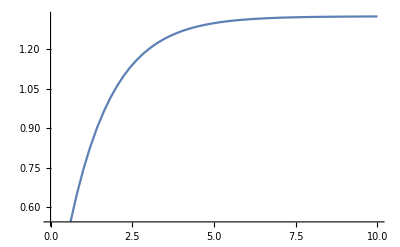

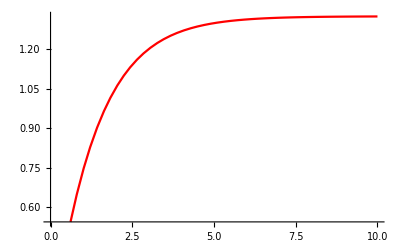

```mathematica
sol=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t]}/.params),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t]}/.params),
th1[0]==0.1,
th2[0]==0.1},{th1,th2},{t,0,100}];
Plot[th1[t]/.sol,{t,0,10}]
Plot[th2[t]/.sol,{t,0,10},PlotStyle->Red]
```

If I strengthen the inhibition, I can get to a situation where the coexistence equilibrium becomes an unstable.

```mathematica
params={β1->1,β2->1,ι12->3,ι21->3,Ι12->1,Ι21->1,σ1->1,σ2->1}
N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]]
Simplify[Tr[D[{dth1,dth2},{{th1,th2}}]]]/.params/.{th1->2.546818276884082,th2->2.5468182768840806}
Simplify[Det[D[{dth1,dth2},{{th1,th2}}]]]/.params/.{th1->2.546818276884082,th2->2.5468182768840806}
```

{β1→1,β2→1,ι12→3,ι21→3,Ι12→1,Ι21→1,σ1→1,σ2→1}

{{th1→0.5+0.866025 ⅈ,th2→0.5-0.866025 ⅈ},{th1→0.5-0.866025 ⅈ,th2→0.5+0.866025 ⅈ},{th1→2.54682,th2→2.54682},{th1→-0.273409-0.563821 ⅈ,th2→-0.273409-0.563821 ⅈ},{th1→-0.273409+0.563821 ⅈ,th2→-0.273409+0.563821 ⅈ}}

-0.442816

-0.141174

Here, you will approach that equilibrium if the system starts out balanced:

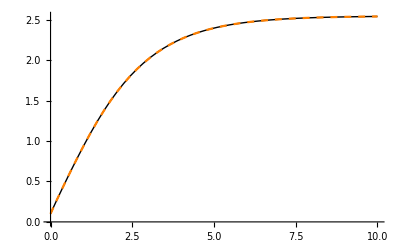

```mathematica
sol=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t]}/.params),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t]}/.params),
th1[0]==0.1,
th2[0]==0.1},{th1,th2},{t,0,100}];
Show[Plot[th1[t]/.sol,{t,0,10},PlotStyle->{Thick,Black}],Plot[th2[t]/.sol,{t,0,10},PlotStyle->{Dashed,Orange}]]
```

But if you start unbalanced at all, one of the responses blows up and the other decays to nothing. I need to modify the model, clearly, to prevent this blowup from happening.

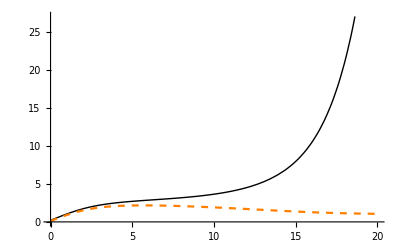

```mathematica
sol=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t]}/.params),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t]}/.params),
th1[0]==0.2,
th2[0]==0.1},{th1,th2},{t,0,100}];
Show[Plot[th1[t]/.sol,{t,0,20},PlotStyle->{Thick,Black}],Plot[th2[t]/.sol,{t,0,20},PlotStyle->{Dashed,Orange}]]
```

We can simplify a bit by assuming that everything is balanced. Then the coexistence equilibrium values will be identical for th1 and th2.

```mathematica
Tr[D[{dth1,dth2},{{th1,th2}}]]/.{th2->th1}
Det[D[{dth1,dth2},{{th1,th2}}]]/.{th2->th1}
```

-2-(th1^2 ι12 (th1+Ι12) σ1)/((th1+th1^2+Ι12+th1 Ι12)^2)+(2 th1 ι12 σ1)/(th1+th1^2+Ι12+th1 Ι12)-(th1^2 ι21 (th1+Ι21) σ2)/((th1+th1^2+Ι21+th1 Ι21)^2)+(2 th1 ι21 σ2)/(th1+th1^2+Ι21+th1 Ι21)

1+(th1^3 ι12 σ1)/((th1+th1^2+Ι12+th1 Ι12)^2)+(th1^2 ι12 Ι12 σ1)/((th1+th1^2+Ι12+th1 Ι12)^2)-(2 th1 ι12 σ1)/(th1+th1^2+Ι12+th1 Ι12)+(th1^3 ι21 σ2)/((th1+th1^2+Ι21+th1 Ι21)^2)+(th1^2 ι21 Ι21 σ2)/((th1+th1^2+Ι21+th1 Ι21)^2)-(2 th1 ι21 σ2)/(th1+th1^2+Ι21+th1 Ι21)-(th1^4 ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21)^2)-(2 th1^5 ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21)^2)+(th1^5 ι12 Ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21)^2)-(2 th1^4 ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12) (th1+th1^2+Ι21+th1 Ι21)^2)+(th1^5 ι12 ι21 Ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21)^2)+(th1^4 ι12 Ι12 ι21 Ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21)^2)-(2 th1^3 ι12 ι21 Ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12) (th1+th1^2+Ι21+th1 Ι21)^2)-(2 th1^4 ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21))-(2 th1^3 ι12 Ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12)^2 (th1+th1^2+Ι21+th1 Ι21))+(4 th1^2 ι12 ι21 σ1 σ2)/((th1+th1^2+Ι12+th1 Ι12) (th1+th1^2+Ι21+th1 Ι21))

#### Consider this model

In this model, I assume that there is a baseline rate of Th1 and Th2 proliferation, specified by the parameter b_i. I assume that self-promotion follows a Hill function with an exponent of 2, as this generates switch-like behavior. This assumption has some support from other models - for example, transcription factor self-promotion (and cross-inhibition) allows has switch-like behavior. I assume that the opposite Th cell population inhibits proliferation, rather than including the opposite as a negative term, which would biologically be interpreted as increasing the loss rate of the opposite Th cell population. And I assume a baseline loss rate of Th cells. These assumptions lead to the following model.

```mathematica
dTh1=b1+(s1 Th1^2)/(S1^2+Th1^2) I12/(I12+Th2) -m Th1;
dTh2=b2+(s2 Th2^2)/(S2^2+Th2^2) I21/(I21+Th1)-m Th2;
```

Because I don’t have a good sense of what the parameters of this model should be, I will nondimensionalize it.

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b1->β1 m S1/.s1->σ1 m S1/.I12->ι12 S2]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b2->β2 m S2/.s2->σ2 m S2/.I21->ι21 S1]//Simplify
```

-th1+β1+(th1^2 ι12 σ1)/((1+th1^2) (th2+ι12))

-th2+β2+(th2^2 ι21 σ2)/((1+th2^2) (th1+ι21))

This is more interpretable. For simplicity, let’s assume that the parameters are balanced between the Th cell populations, so there is no intrinsic bias towards either a Th1 or Th2 response. 

The parameter β_i=b_i/(m S_i) is the baseline immune supply rate divided by the rate that immune cells are depleted when at half the density that promotes maximal immune proliferation. The parameter σ_i=s_i/(m S_i) is the maximum immune proliferation rate divided by the same rate. Thus, rather than worrying excessively about the absolute values of these parameters, the more important thing is their relative value, with needing σ_i>>β_i since self-stimulated immune proliferation should be much higher than baseline immune supply. 

The parameter ι_ij=i_ij/I_ij is the ratio of the minimum inhibition of Th_j cells on Th_i proliferation to the number of Th_j cells where inhibition is half is maximal value (of 0). Thus this parameter must be less than 0 (if the minimum inhibition is greater than 1, Th_j cells actually fuel Th_i proliferation). 

η_i=S_i/I_ji gives the ratio of the half-maxima for self-stimulated proliferation by Th_i to cross-inhibition by Th_i on Th_j. This should also presumably be less than 1, reflecting that self-promotion is greater than cross-inhibition.

The form of the isoclines can give good insight into the possible dynamics of the system.

```mathematica
th1isocline=Solve[dth1==0,th2]//Simplify
th2isocline=Solve[dth2==0,th1]//Simplify
```

{{th2→(ι12 (-th1-th1^3+β1+th1^2 (β1+σ1)))/((1+th1^2) (th1-β1))}}

{{th1→(ι21 (-th2-th2^3+β2+th2^2 (β2+σ2)))/((1+th2^2) (th2-β2))}}

Note that the lines th1=0 and th2=0 are not isoclines for this system because of baseline Th cell-independent proliferation.  This is important because it means that only the intersections of the two lines above are possible equilibria of the system. In order to have multi-stability, the isoclines must cross at multiple places. This will be most easily facilitated by the slope of the isoclines changing signs.

Taking the derivatives of the isoclines with respect to the Th cell populations, you can see that the baseline immune supply parameters β_i are critical in determining the shape of the isocline.

```mathematica
Simplify[D[th1isocline[[1,1,2]],th1]]
Simplify[D[th2isocline[[1,1,2]],th2]]
```

-(th1 (-th1+th1^3+2 β1) ι12 σ1)/((1+th1^2)^2 (th1-β1)^2)

-(th2 (-th2+th2^3+2 β2) ι21 σ2)/((1+th2^2)^2 (th2-β2)^2)

Numerically solving for the zeros of these isoclines, you can see that the slope of the isoclines will only change signs if β_i is quite small, in which case there are multiple zeros, indicating that the isocline changes direction multiple times. If β_i is large, however, there are no zeros in the positive real plane, indicating that the slope will have a constant sign, which will limit the opportunities for multi-stability, as the most likely scenario is that the isoclines will cross only at a single point. 

This actually makes sense biologically: if the baseline immune supply rate is high, that makes polarization unlikely as the system will constantly be stimulating the proliferation of both Th cell subpopulations.

```mathematica
Table[N[Solve[(th1-th1^3-2 β1)==0,th1]],{β1,0,0.25,0.05}]
```

{{{th1→-1.},{th1→0.},{th1→1.}},{{th1→-1.04668},{th1→0.101031},{th1→0.945649}},{{th1→-1.08803},{th1→0.209149},{th1→0.878885}},{{th1→-1.12542},{th1→0.338936},{th1→0.786483}},{{th1→-1.1597},{th1→0.579852-0.0932014 ⅈ},{th1→0.579852+0.0932014 ⅈ}},{{th1→-1.19149},{th1→0.595744-0.254426 ⅈ},{th1→0.595744+0.254426 ⅈ}}}

```mathematica
N[Sqrt[3/81]]
```

0.19245

```mathematica
N[Simplify[Solve[th1-th1^3-2 β1==0,th1]]]
```

{{th1→-(0.48075 (1.44225+(9. β1+√(-3.+81. β1^2))^(2/3)))/((9. β1+√(-3.+81. β1^2))^(1/3))},{th1→(0.240375 ((1.44225+2.49805 ⅈ)+(1.-1.73205 ⅈ) (9. β1+√(-3.+81. β1^2))^(2/3)))/((9. β1+√(-3.+81. β1^2))^(1/3))},{th1→(0.240375 ((1.44225-2.49805 ⅈ)+(1.+1.73205 ⅈ) (9. β1+√(-3.+81. β1^2))^(2/3)))/((9. β1+√(-3.+81. β1^2))^(1/3))}}

Here are a set of parameters that show the most multi-stability that is possible in this system. The filled black circles show the stable equilibria, and the open circles show the unstable equilibria. You can see that there 4 stable equilibria, corresponding to a low (but balanced) co-expression equilibrium, a high Th1/Th2 co-expression equilibrium, and the two polarized equilibria.

{{th1→0.167811,th2→1.45729},{th1→0.180241,th2→0.446222},{th1→0.184947,th2→0.184947},{th1→0.446222,th2→0.180241},{th1→0.494769,th2→0.494769},{th1→0.678821,th2→1.28958},{th1→1.12255,th2→1.12255},{th1→1.28958,th2→0.678821},{th1→1.45729,th2→0.167811}}

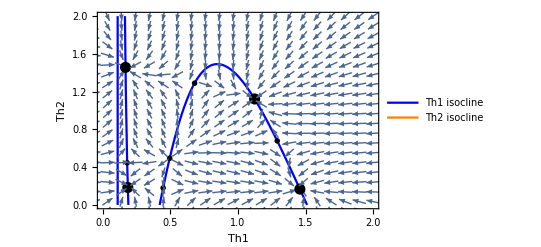

```mathematica
params={σ1->2,σ2->2,β1->0.12,β2->0.12,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

If you weaken the baseline response, you lose the high co-expression equilibrium, and end up with only three stable equilibria representing low co-expression or polarization.

{{th1→0.0960798,th2→1.37689},{th1→0.0979588,th2→0.585035},{th1→0.0993591,th2→0.0993591},{th1→0.585035,th2→0.0979588},{th1→0.752926,th2→0.752926},{th1→0.914991,th2→0.914991},{th1→1.37689,th2→0.0960798}}

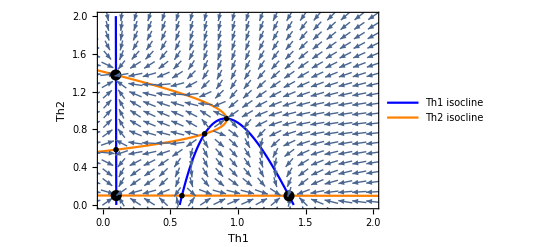

```mathematica
params={σ1->2,σ2->2,β1->0.08,β2->0.08,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.01,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.01,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

But if you strengthen the baseline immune response, you end up with three equilibria representing polarization and high co-expression. Any further strengthening and the only stable equilibrium is high co-expression.

{{th1→0.260646,th2→1.49875},{th1→0.49988,th2→1.4281},{th1→1.2102,th2→1.2102},{th1→1.4281,th2→0.49988},{th1→1.49875,th2→0.260646}}

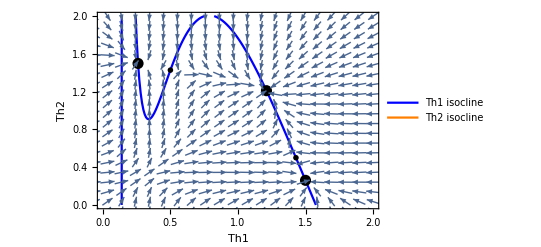

```mathematica
params={σ1->2,σ2->2,β1->0.15,β2->0.15,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.01,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.01,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

Strengthening cross-inhibition:

{{th1→0.160669,th2→1.42531},{th1→0.175447,th2→0.462892},{th1→0.18268,th2→0.18268},{th1→0.462892,th2→0.175447},{th1→0.588251,th2→0.588251},{th1→0.88865,th2→0.88865},{th1→1.42531,th2→0.160669}}

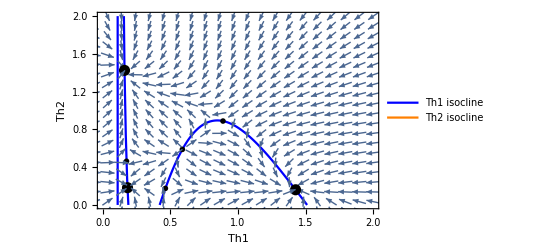

```mathematica
params={σ1->2,σ2->2,β1->0.12,β2->0.12,ι12->6,ι21->6};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

Strengthening cross-inhibition:

{{th1→0.172799,th2→1.47405},{th1→0.18291,th2→0.437772},{th1→0.186186,th2→0.186186},{th1→0.437772,th2→0.18291},{th1→0.465626,th2→0.465626},{th1→0.575729,th2→1.38783},{th1→1.2381,th2→1.2381},{th1→1.38783,th2→0.575729},{th1→1.47405,th2→0.172799}}

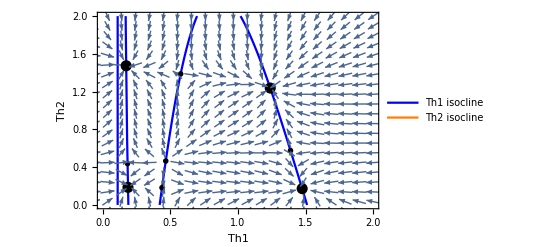

```mathematica
params={σ1->2,σ2->2,β1->0.12,β2->0.12,ι12->15,ι21->15};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

Strengthening self-promotion:

{{th1→0.197032,th2→2.12833},{th1→0.373799,th2→2.07608},{th1→1.71132,th2→1.71132},{th1→2.07608,th2→0.373799},{th1→2.12833,th2→0.197032}}

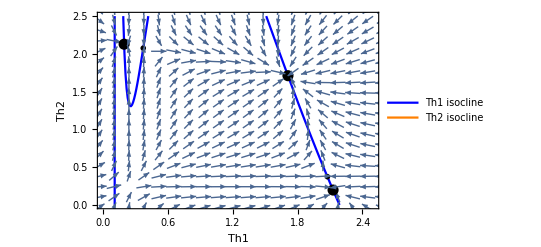

```mathematica
params={σ1->2.5,σ2->2.5,β1->0.12,β2->0.12,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2.5},{0,2.5}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

{{th1→0.161368,th2→1.04283},{th1→0.164297,th2→0.680422},{th1→0.169345,th2→0.169345},{th1→0.680422,th2→0.164297},{th1→1.04283,th2→0.161368}}

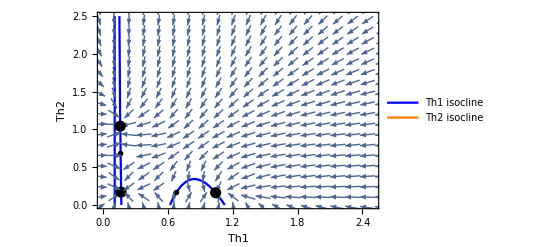

```mathematica
params={σ1->1.8,σ2->1.8,β1->0.12,β2->0.12,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2.5},{0,2.5}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

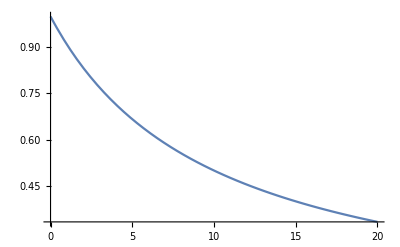

```mathematica
Plot[10/(10+x),{x,0,20}]
```

#### Can you get similar behavior with a simpler model?

The only difference here is the Hill function with an exponent of 1 for self-stimulation, which is also supported by previous analyses - in particular, transcription factor promotion of cytokine expression is smooth, rather than switch-like.

```mathematica
dTh1=b1+(s1 Th1)/(S1+Th1) I12/(I12+Th2) -m Th1;
dTh2=b2+(s2 Th2)/(S2+Th2) I21/(I21+Th1)-m Th2;
```

This model can be nondimensionalized identically to the previous model.

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b1->β1 m S1/.s1->σ1 m S1/.I12->ι12 S2]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b2->β2 m S2/.s2->σ2 m S2/.I21->ι21 S1]//Simplify
```

β1+th1 (-1+(ι12 σ1)/(th2+th1 th2+ι12+th1 ι12))

β2+th2 (-1+(ι21 σ2)/(th1+th1 th2+ι21+th2 ι21))

This is more interpretable. For simplicity, let’s assume that the parameters are balanced between the Th cell populations, so there is no intrinsic bias towards either a Th1 or Th2 response. 

The parameter β_i=b_i/(m S_i) is the baseline immune supply rate divided by the rate that immune cells are depleted when at half the density that promotes maximal immune proliferation. The parameter σ_i=s_i/(m S_i) is the maximum immune proliferation rate divided by the same rate. Thus, rather than worrying excessively about the absolute values of these parameters, the more important thing is their relative value, with needing σ_i>>β_i since self-stimulated immune proliferation should be much higher than baseline immune supply. 

ι_ij=S_i/I_ji gives the ratio of the half-maxima for self-stimulated proliferation by Th_i to cross-inhibition by Th_i on Th_j. This should also presumably be less than 1, reflecting that self-promotion is greater than cross-inhibition.

The form of the isoclines can give good insight into the possible dynamics of the system.

```mathematica
th1isocline=Solve[dth1==0,th2]//Simplify
th2isocline=Solve[dth2==0,th1]
```

{{th2→(ι12 (-th1^2+β1+th1 (-1+β1+σ1)))/((1+th1) (th1-β1))}}

{{th1→(-th2 ι21-th2^2 ι21+β2 ι21+th2 β2 ι21+th2 ι21 σ2)/((1+th2) (th2-β2))}}

```mathematica
Simplify[-th1^2+β1+th1 (-1+β1+σ1)/.th1->β1]
```

β1 σ1

Note that the lines th1=0 and th2=0 are not isoclines for this system because of baseline Th cell-independent proliferation.  This is important because it means that only the intersections of the two lines above are possible equilibria of the system. In order to have multi-stability, the isoclines must cross at multiple places. This will be most easily facilitated by the slope of the isoclines changing signs.

Taking the derivatives of the isoclines with respect to the Th cell populations, you can see that, with this model, the slopes of the isoclines are both always negative, regardless of any other parameter value. This means that any potential for multistability will be pretty blunted.

```mathematica
Simplify[D[th1isocline[[1,1,2]],th1]]
Simplify[D[th2isocline[[1,1,2]],th2]]
```

-((th1^2+β1) ι12 σ1)/((1+th1)^2 (th1-β1)^2)

-((th2^2+β2) ι21 σ2)/((1+th2)^2 (th2-β2)^2)

To evaluate the potential for multiple intersections, we need to have a clearer sense of the shape by looking at the second derivative. If the sign of the second derivative also remains constant, then the function will, overall, have a simple shape, and there will essentially be no possibility of multistability.

For th_i>β_i, the second derivative will be positive. Thus both isoclines have a simple shape: a function with a negative slope but a positive second derivative has a shape like e^-x. Two such curves will only ever be able to intersect in one place. Thus there is no possibility for multistability in this model.

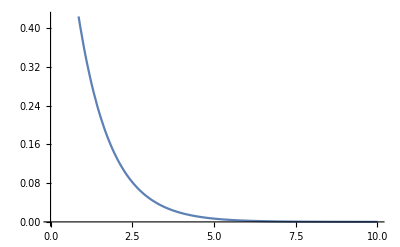

```mathematica
Plot[Exp[-x],{x,0,10}]
```

```mathematica
Simplify[D[th1isocline[[1,1,2]],{th1,2}]]//Simplify
Simplify[D[th2isocline[[1,1,2]],{th2,2}]]
```

(2 (th1^3+β1+3 th1 β1-β1^2) ι12 σ1)/((1+th1)^3 (th1-β1)^3)

(2 (th2^3+β2+3 th2 β2-β2^2) ι21 σ2)/((1+th2)^3 (th2-β2)^3)

#### What about a model where inhibition is stronger?

In this model, there is very strong inhibition between Th cell populations, but smooth self-promotion.

```mathematica
dTh1=b1+(s1 Th1)/(S1+Th1) I12^2/(I12^2+Th2^2) -m Th1;
dTh2=b2+(s2 Th2)/(S2+Th2) I21^2/(I21^2+Th1^2)-m Th2;
```

This model can be nondimensionalized similarly to previous models:

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b1->β1 m S1/.s1->σ1 m S1/.I12->ι12 S2]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b2->β2 m S2/.s2->σ2 m S2/.I21->ι21 S1]//Simplify
```

β1+th1 (-1+(ι12^2 σ1)/((1+th1) (th2^2+ι12^2)))

β2+th2 (-1+(ι21^2 σ2)/((1+th2) (th1^2+ι21^2)))

The isoclines are harder to interpret.

```mathematica
th1isocline=Solve[dth1==0,th2]⟦2⟧//Simplify
th2isocline=Solve[dth2==0,th1]⟦2⟧//Simplify
```

{th2→(ι12 √(th1^2-β1-th1 (-1+β1+σ1)))/(√(-(1+th1) (th1-β1)))}

{th1→(ι21 √(th2^2-β2-th2 (-1+β2+σ2)))/(√(-(1+th2) (th2-β2)))}

However, it must be the case that the Th abundance is below a critical value for the numerator to be real, and above β_i for the denominator to be real. In particular, if th1 > β_1, then the numerator and denominator will both be positive real numbers, and the isocline will exist. Basically, this model has a limited portion of state space where the isoclines will exist.

```mathematica
(* The value of the numerator if th1 = β1 *)
Simplify[-th1^2+β1+th1 (-1+β1+ι12 σ1)/.th1->β1]
```

β1 ι12 σ1

Taking the derivatives of the isoclines with respect to the Th cell populations are a bit hard to interpret, initially, because of the square root term in the denominator. However, that square root term also appears in the equation for the isocline itself, and we know that it must be positive, which means that, for any portion of state space where the isoclines exist,they will have a negative slope.

```mathematica
Simplify[D[th1isocline⟦1,2⟧,th1]] 
Simplify[D[th2isocline⟦1,2⟧,th2]]
```

-((th1^2+β1) ι12 σ1)/(2 (-(1+th1) (th1-β1))^(3/2) √(th1^2-β1-th1 (-1+β1+σ1)))

-((th2^2+β2) ι21 σ2)/(2 (-(1+th2) (th2-β2))^(3/2) √(th2^2-β2-th2 (-1+β2+σ2)))

The shape of these isoclines is hard to interpret, but it appears clear that the shape is not simple, as it was above. If the shape is complex enough, it is possible to get multistability.

```mathematica
Simplify[D[th1isocline⟦1,2⟧,{th1,2}]] //FullSimplify
Simplify[D[th2isocline⟦1,2⟧,{th2,2}]]
```

(ι12 σ1 (-4 (1+th1) (th1-β1) (th1^3+β1+3 th1 β1-β1^2)+(3 th1^4+2 th1 (2+5 th1) β1-(1+4 th1) β1^2) σ1))/(4 (-(1+th1) (th1-β1))^(5/2) ((1+th1) (th1-β1)-th1 σ1)^(3/2))

-((ι21 σ2 (4 th2^5+8 th2^3 β2+th2^4 (4-4 β2-3 σ2)+4 th2 β2 (1+β2^2+β2 (-5+σ2)-σ2)+β2^2 (-4+4 β2+σ2)-2 th2^2 β2 (-8+8 β2+5 σ2)))/(4 (-(1+th2) (th2-β2))^(5/2) (th2^2-β2-th2 (-1+β2+σ2))^(3/2)))

```mathematica
Solve[(-4 (1+th1) (th1-β1) (th1^3+β1+3 th1 β1-β1^2)+(3 th1^4+2 th1 (2+5 th1) β1-(1+4 th1) β1^2) σ1)==0,th1]
```

{{th1→Root[-4 β1^2+4 β1^3+β1^2 σ1+(4 β1-20 β1^2+4 β1^3-4 β1 σ1+4 β1^2 σ1) #1+(16 β1-16 β1^2-10 β1 σ1) #1^2+8 β1 #1^3+(4-4 β1-3 σ1) #1^4+4 #1^5&,1]},{th1→Root[-4 β1^2+4 β1^3+β1^2 σ1+(4 β1-20 β1^2+4 β1^3-4 β1 σ1+4 β1^2 σ1) #1+(16 β1-16 β1^2-10 β1 σ1) #1^2+8 β1 #1^3+(4-4 β1-3 σ1) #1^4+4 #1^5&,2]},{th1→Root[-4 β1^2+4 β1^3+β1^2 σ1+(4 β1-20 β1^2+4 β1^3-4 β1 σ1+4 β1^2 σ1) #1+(16 β1-16 β1^2-10 β1 σ1) #1^2+8 β1 #1^3+(4-4 β1-3 σ1) #1^4+4 #1^5&,3]},{th1→Root[-4 β1^2+4 β1^3+β1^2 σ1+(4 β1-20 β1^2+4 β1^3-4 β1 σ1+4 β1^2 σ1) #1+(16 β1-16 β1^2-10 β1 σ1) #1^2+8 β1 #1^3+(4-4 β1-3 σ1) #1^4+4 #1^5&,4]},{th1→Root[-4 β1^2+4 β1^3+β1^2 σ1+(4 β1-20 β1^2+4 β1^3-4 β1 σ1+4 β1^2 σ1) #1+(16 β1-16 β1^2-10 β1 σ1) #1^2+8 β1 #1^3+(4-4 β1-3 σ1) #1^4+4 #1^5&,5]}}

Numerical exploration shows that the same of these isoclines is such that, even though both isoclines always have a negative slope, it is possible for them to intersect in multiple places, leading to multistability.

Here is an example of such a set of parameters. With this set of parameters, the only stable equilibria represent polarized immune responses, so either Th1 or Th2 will dominate, but there is no low-activation equilibrium and no co-expression equilibrium. This makes sense, intuitively, given that cross-inhibition is stronger than self-promotion: one response must end up inhibited while the other dominates the immune cell population.

```mathematica
N[1/Sqrt[2]]
```

0.707107

```mathematica
Sqrt[0.15/2]
```

0.273861

{{th1→0.0188568,th2→2.51274},{th1→0.918777,th2→0.918777},{th1→2.51274,th2→0.0188568}}

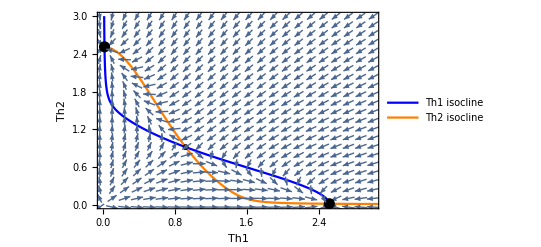

```mathematica
params={σ1->3.5,σ2->3.5,β1->0.01,β2->0.01,ι12->1,ι21->1};eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,2⟧/.params},{th1,0,4,0.001}],PlotRange->{{0,3},{0,3}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

However, if you greatly weaken cross-inhibition (in this case by reducing the value of ι_ij, then you can end up with a single stable co-expression equilibrium.

{{th1→1.71617,th2→1.71617}}

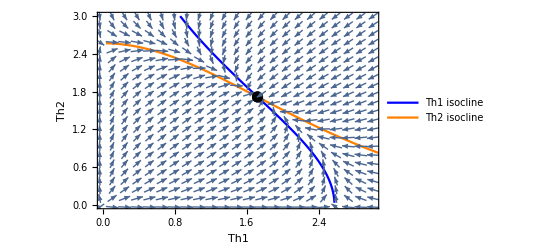

```mathematica
params={σ1->3.5,σ2->3.5,β1->0.05,β2->0.05,ι12->3,ι21->3};eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,2⟧/.params},{th1,0,4,0.001}],PlotRange->{{0,3},{0,3}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

On the other hand, if you weaken cross-inhibition by reducing the value of ι_ij, you end up with a single stable equilibrium representing a low co-expression equilibrium.

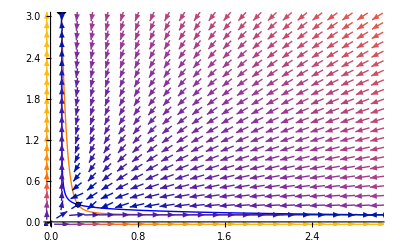

```mathematica
params={σ1->20,σ2->20,β1->0.1,β2->0.1,ι12->0.05,ι21->0.05,η1->2,η2->2};eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧;
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,2⟧/.params},{th1,0,4,0.001}],PlotRange->{{0,3},{0,3}},PlotStyle->{Thick,Blue}],
ListLinePlot[Table[{th2isocline⟦1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorStyle->{Gray},VectorPoints->30]
]
```

#### Final model

In this one, I allow for a slightly different functional form. Basically I have a function that controls the strength of self-promotion, with inhibition.

```mathematica
dTh1=b1+(s1 Th1)/(S1+Th1) i12/(i12+Th2) Th1-m Th1;
dTh2=b2+(s2 Th2)/(S2+Th2) i21/(i21+Th1)Th2-m Th2;
```

Nondimensionalize:

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2})/.TH1hat->S1/.TH2hat->S2/.that->1/m/.i12->ι12 S2 /.b1->β1 m S1/.s1->σ1 m]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2})/.TH1hat->S1/.TH2hat->S2/.that->1/m/.i21->ι21 S1 /.b2->β2 m S2/.s2->σ2 m]//Simplify
```

-th1+β1+(th1^2 ι12 σ1)/(th2+th1 th2+ι12+th1 ι12)

-th2+β2+(th2^2 ι21 σ2)/(th1+th1 th2+ι21+th2 ι21)

The form of the isoclines is instructive, as always.

```mathematica
th1isocline=Solve[dth1==0,th2]//FullSimplify
th2isocline=Solve[dth2==0,th1]//FullSimplify
```

{{th2→(ι12 (β1+th1 (-1+β1+th1 (-1+σ1))))/((1+th1) (th1-β1))}}

{{th1→(ι21 (β2+th2 (-1+β2+th2 (-1+σ2))))/((1+th2) (th2-β2))}}

```mathematica
(β1+th1 (-1+β1+th1 (-1+σ1)))/.th1->β1//Simplify
```

β1^2 σ1

Here you can see that the slope of the isoclines changes sign, but only if the baseline activation is fairly small (β_i<1). This fits with the intuition developed above for the first model.

```mathematica
Simplify[D[th1isocline⟦1,1,2⟧,th1]]
Simplify[D[th2isocline⟦1,1,2⟧,th2]]
Solve[Simplify[D[th1isocline⟦1,1,2⟧,th1]]==0,th1]
Solve[Simplify[D[th2isocline⟦1,1,2⟧,th2]]==0,th2]
```

-(th1 (th1 (-1+β1)+2 β1) ι12 σ1)/((1+th1)^2 (th1-β1)^2)

-(th2 (th2 (-1+β2)+2 β2) ι21 σ2)/((1+th2)^2 (th2-β2)^2)

{{th1→0},{th1→-(2 β1)/(-1+β1)}}

{{th2→0},{th2→-(2 β2)/(-1+β2)}}

```mathematica
Simplify[Simplify[D[th1isocline⟦1,1,2⟧,{th1,2}]]/.th1->-β1/(-1+β1)]
```

(2 (-1+β1)^4 (1+β1^2) ι12 σ1)/β1^4

```mathematica
-(th1 (th1 (-1+β1)+2 β1) ι12 σ1)/((1+th1)^2 (th1-β1)^2)/.th1->-β1/(-1+β1)
```

(β1^2 ι12 σ1)/((-1+β1) (1-β1/(-1+β1))^2 (-β1-β1/(-1+β1))^2)

You can see that there are multiple equilibria here, but only one that is stable (a low activation equilibrium). Otherwise what happens is runaway stimulation. The positive self-promotion overwhelms cross-inhibition and the system is either stable at a low co-expression equilibrium, or it blows up. That is clearly infeasible.

{{th1→0.0526316,th2→1.},{th1→0.0555366,th2→0.0555366},{th1→1.,th2→0.0526316}}

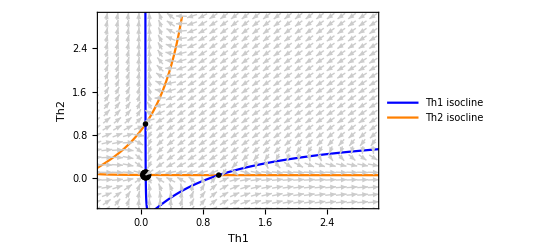

```mathematica
params={β1->0.05,β2->0.05,ι12->1,ι21->1,σ1->2,σ2->2};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange},PlotRange->{{-0.5,3},{-0.5,3}}],
ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0,4,0.001}],PlotStyle->{Thick,Blue},PlotRange->All,PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorPoints->30,VectorColorFunction->None,VectorStyle->GrayLevel[0.8]],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

{{th1→0.068575,th2→0.18459},{th1→0.0733501,th2→0.0733501},{th1→0.18459,th2→0.068575},{th1→0.25,th2→0.25},{th1→2.72665,th2→2.72665}}

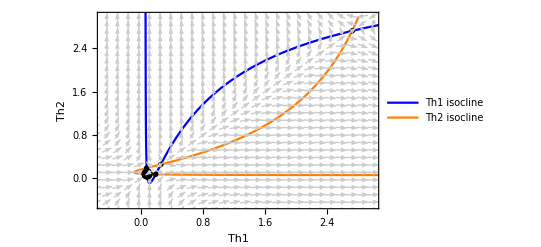

```mathematica
params={β1->0.05,β2->0.05,ι12->1,ι21->1,σ1->5,σ2->5};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]]
(* stable equilibria have a positive determinant and a negative trace *)
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧;
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange},PlotRange->{{-0.5,3},{-0.5,3}}],
ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0,4,0.001}],PlotStyle->{Thick,Blue},PlotRange->All,PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorPoints->30,VectorColorFunction->None,VectorStyle->GrayLevel[0.8]],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

{β1→0.07,β2→0.04,ι12→1,ι21→1,σ1→5,σ2→5}

{{th1→0.123625-0.0574354 ⅈ,th2→0.0509303+0.000964718 ⅈ},{th1→0.123625+0.0574354 ⅈ,th2→0.0509303-0.000964718 ⅈ},{th1→0.137079,th2→0.231785},{th1→0.178474,th2→0.245874},{th1→2.72184,th2→2.7531}}

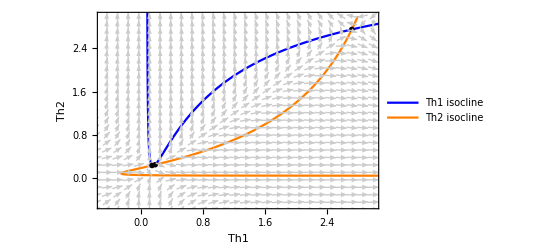

```mathematica
params={β1->0.07,β2->0.04,ι12->1,ι21->1,σ1->5,σ2->5}
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]]
(* stable equilibria have a positive determinant and a negative trace *)
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧;
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange},PlotRange->{{-0.5,3},{-0.5,3}}],
ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0,4,0.001}],PlotStyle->{Thick,Blue},PlotRange->All,PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorPoints->30,VectorColorFunction->None,VectorStyle->GrayLevel[0.8]],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

```mathematica
?LegendLabel
```

```mathematica
?VectorPlot
```

{β1→2,β2→2,ι12→1,ι21→1,Ι12→1,Ι21→1,σ1→20,σ2→20}

{{th1→0.0294118-0.341734 ⅈ,th2→0.0294118+0.341734 ⅈ},{th1→0.0294118+0.341734 ⅈ,th2→0.0294118-0.341734 ⅈ},{th1→20.1538,th2→20.1538},{th1→-0.0768897-0.305491 ⅈ,th2→-0.0768897-0.305491 ⅈ},{th1→-0.0768897+0.305491 ⅈ,th2→-0.0768897+0.305491 ⅈ}}

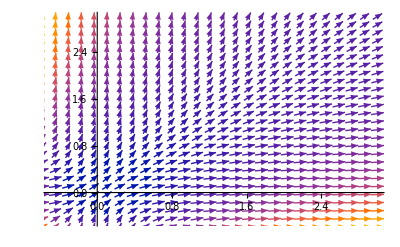

```mathematica
params={β1->2,β2->2,ι12->1,ι21->1,Ι12->1,Ι21->1,σ1->20,σ2->20}
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]]
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧;
Show[ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0,4,0.001}],PlotStyle->{Thick,Orange},PlotRange->{{-0.5,3},{-0.5,3}}],
ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0,4,0.001}],PlotStyle->{Thick,Blue},PlotRange->All],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorStyle->{Gray},VectorPoints->30]]
```